# Problem Sheet 03

## Lab Report by Rafsan Al Mamun

```mathematica
for[x_]:=E^x*Sin[x]
```

```mathematica
fos[x_]:=Log[E^x+E^-x]
```

```mathematica
f[x_,y_]:=Sin[x^2+y^2]
```

```mathematica
g[x_,y_]:=ArcTan[y/x]
```

```mathematica
Sum[n,{n,1,100}]
```

5050

```mathematica
Sum[i^2,{i,1,n}]
```

1/6 n (1+n) (1+2 n)

```mathematica
Sum[2n+1,{n,0,49}]
```

2500

```mathematica
Sum[1/2^n,{n,0,Infinity}]
```

2

```mathematica
Sum[j,{i,1,7},{j,1,i}]
```

84

```mathematica
Product[n^2,{n,1,6}]
```

518400

```mathematica
Product[2j,{i,1,4},{j,1,i}]
```

294912

```mathematica
FormulaOfSummation[x_]:=Sum[i^x,{i,1,n}]
```

```mathematica
FormulaOfSummation[1]
```

1/2 n (1+n)

```mathematica
FormulaOfSummation[2]
```

1/6 n (1+n) (1+2 n)

```mathematica
FormulaOfSummation[3]
```

1/4 n^2 (1+n)^2

```mathematica
Solve[x^2+9x+2==0,x]
```

{{x→1/2 (-9-√73)},{x→1/2 (-9+√73)}}

```mathematica
Solve[a*x^2+b*x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
Solve[a*x^3+b*x^2+c*x+d==0,x]
```

{{x→-b/(3 a)-(2^(1/3) (-b^2+3 a c))/(3 a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))+((-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))/(3 2^(1/3) a)},{x→-b/(3 a)+((1+ⅈ √3) (-b^2+3 a c))/(3 2^(2/3) a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))-((1-ⅈ √3) (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))/(6 2^(1/3) a)},{x→-b/(3 a)+((1-ⅈ √3) (-b^2+3 a c))/(3 2^(2/3) a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))-((1+ⅈ √3) (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))/(6 2^(1/3) a)}}

```mathematica
Solve[x^5+16 x^4+7 x^3+17 x^2+11x+5==0,x]
```

{{x→Root[5+11 #1+17 #1^2+7 #1^3+16 #1^4+#1^5&,1]},{x→Root[5+11 #1+17 #1^2+7 #1^3+16 #1^4+#1^5&,2]},{x→Root[5+11 #1+17 #1^2+7 #1^3+16 #1^4+#1^5&,3]},{x→Root[5+11 #1+17 #1^2+7 #1^3+16 #1^4+#1^5&,4]},{x→Root[5+11 #1+17 #1^2+7 #1^3+16 #1^4+#1^5&,5]}}

```mathematica
Solve[Sin[ArcCos[x^2-x]]==1,x]
```

{{x→0},{x→1}}

```mathematica
Solve[{5 x^2+6 y^2==9,x+y==1},{x,y}]
```

{{x→1/11 (6-√69),y→1/11 (5+√69)},{x→1/11 (6+√69),y→1/11 (5-√69)}}

```mathematica
Solve[{x+y+z==9,x+4y==4,2x+3y+z==9},{x,y,z}]
```

{{x→-4,y→2,z→11}}

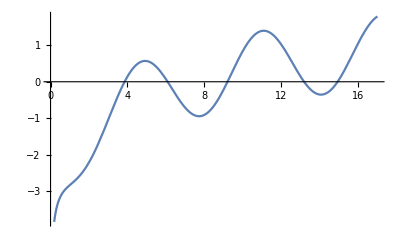

```mathematica
Plot[Log[x]-Sin[x]-2,{x,0,17}]
```

```mathematica
FindRoot[Log[x]-Sin[x]==2,{x,4}]
```

{x→3.85128}

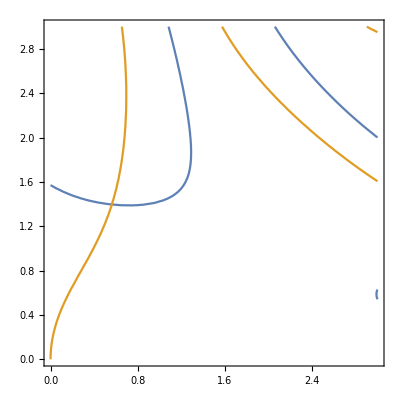

```mathematica
ContourPlot[{Sin[x*y]-Sin[x]-Cos[y],Cos[x*y]-Sin[x]-Cos[y]},{x,0,3},{y,0,3}]
```

```mathematica
FindRoot[{Sin[x*y]==Sin[x]+Cos[y],Cos[x*y]==Sin[x]+Cos[y]},{x,0.6},{y,1.4}]
```

{x→0.562547,y→1.39615}